```mathematica
(*test*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\benjamin\Documents\FPII\Moessbauer\code

```mathematica
x={3.01,1.00,0.21,1.95,7.97,0.46,0.66,0.88,1.22,1.43,1.67,1.87,2.16,2.51,3.99,4.98,6.49,9.43,10.92,12.43 };
names={"3.01","1.00","0.21","1.95","7.97","0.46","0.66","0.88","1.22","1.43","1.67","1.87","2.16","2.51","3.99","4.98","6.49","9.43","10.92","12.43"};
```

```mathematica
files=Flatten[Import[StringJoin["../data/background/",#,"mm.TKA"],"CSV"]]&/@names;
```

```mathematica
Dimensions[files]
```

{20,2048}

```mathematica
data=Table[{x[[j]],Sum[files[[j]][[90;;250]][[i]],{i,1,161}]/600.},{j,1,Length[files]}];
```

```mathematica
liplot=ListPlot[data];
```

```mathematica
model = a Exp[-b v]+c Exp[-d v];
```

```mathematica
nlm= NonlinearModelFit[data, model, {a,b,c,d}, v];
nlm["BestFit"]
```

16.5109 ⅇ^(-1.86792 v)+29.738 ⅇ^(-0.0331478 v)

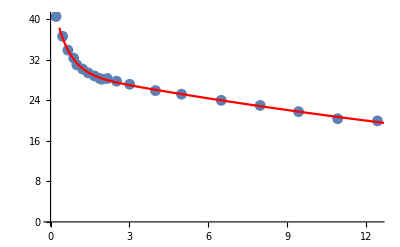

```mathematica
fit=Plot[nlm["BestFit"],{v,0,14}, PlotStyle->Red];
Show[{liplot,fit}]
```

```mathematica
nlm["CorrelationMatrix"]//MatrixForm
```

(1. | 0.862715 | 0.111216 | 0.761803
0.862715 | 1. | 0.0425748 | 0.596468
0.111216 | 0.0425748 | 1. | 0.614734
0.761803 | 0.596468 | 0.614734 | 1.)

```mathematica
nlm[0](*Extrapoliere Untergrund*)
```

46.249

```mathematica
nplates={1,1,1,1,2,2,3,4,2,3,2,3,2,1,1,2,2,3,4,4};
yerror=Sqrt[#]/600&/@Table[Sum[files[[j]][[90;;250]][[i]],{i,1,161}],{j,1,Length[files]}];
```

```mathematica
exporttable=Table[Join[data[[i]],{Sqrt[nplates[[i]]]*0.01,yerror[[i]]}],{i,1,Length[files]}]//N;
```

```mathematica
Export["../data/background/data.csv",exporttable,"Table"];
```